```mathematica
endpoint=10000
```

10000

```mathematica
a=-0.2
```

-0.2

```mathematica
hamil[x_]=-PauliMatrix[3]/2-1/2(a Cos[x])PauliMatrix[1]
```

{{-0.5,0.1 Cos[x]},{0.1 Cos[x],0.5}}

```mathematica
waveAkh[x_]={waveAkh1[x],waveAkh2[x]};
```

```mathematica
initwaveAkh={1,0}
```

{1,0}

```mathematica
sol=NDSolve[{I D[waveAkh[x],x]==hamil[x].waveAkh[x],waveAkh[0]==initwaveAkh},waveAkh[x],{x,0,endpoint}];
```

```mathematica
solList=Table[{x,Abs[waveAkh2[x]]^2/.First@sol},{x,0,endpoint/100,0.01}];
```

```mathematica
predList=Table[{x,Sin[a x/4]^2},{x,0,endpoint/100,0.01}]
```

{{0.,0.},{0.01,2.5×10^-7},{0.02,1.×10^-6},{0.03,2.25×10^-6},{0.04,3.99999×10^-6},9991,{99.96,0.92062},{99.97,0.92035},{99.98,0.920079},{99.99,0.919808},{100.,0.919536}}
 |  |  |  |

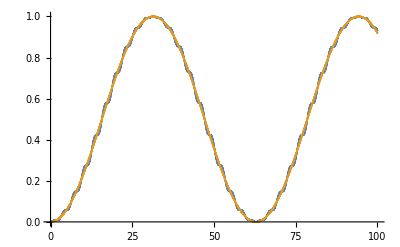

```mathematica
ListPlot[
{solList,predList}
]
```